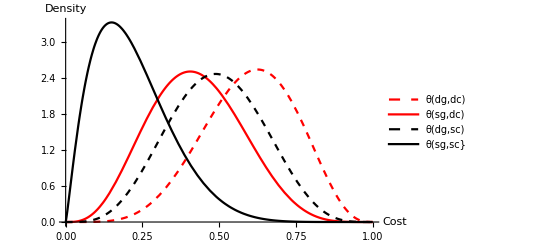

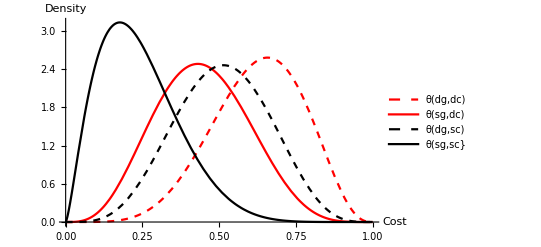

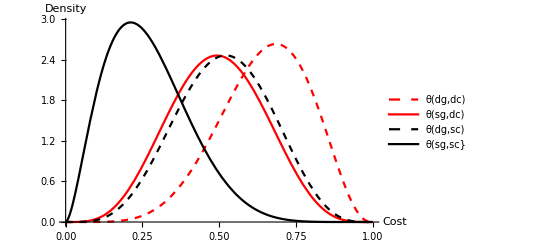

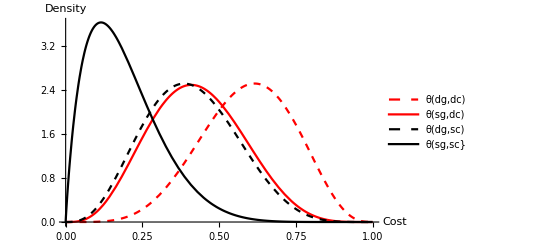

/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Ct0.png

/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Ct1.png

/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Tt0.png

/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Tt1.png

```mathematica
p1=Plot[Table[PDF[BetaDistribution[a,10-a],x],{a,{6.003,4.247,4.909,2.197}}]//Evaluate,{x,0,1},PlotStyle->{{Dashed,Red},{Line,Red},{Dashed,Black},{Line,Black}},AxesLabel->{Cost,Density},PlotLegends->Placed[{"θ(dg,dc)","θ(sg,dc)","θ(dg,sc)","θ(sg,sc}"},Below]]
p2=Plot[Table[PDF[BetaDistribution[a,10-a],x],{a,{6.261,4.447,5.114,2.413}}]//Evaluate,{x,0,1},
AxesLabel->{Cost,Density},PlotStyle->{{Dashed,Red},{Line,Red},{Dashed,Black},{Line,Black}},PlotLegends->Placed[{"θ(dg,dc)","θ(sg,dc)","θ(dg,sc)","θ(sg,sc}"},Below]]
p3=Plot[Table[PDF[BetaDistribution[a,10-a],x],{a,{6.481,4.945,5.172,2.695}}]//Evaluate,{x,0,1},
AxesLabel->{Cost,Density},PlotStyle->{{Dashed,Red},{Line,Red},{Dashed,Black},{Line,Black}},PlotLegends->Placed[{"θ(dg,dc)","θ(sg,dc)","θ(dg,sc)","θ(sg,sc}"},Below]]
p4=Plot[Table[PDF[BetaDistribution[a,10-a],x],{a,{5.925,4.275,4.088,1.922}}]//Evaluate,{x,0,1},
AxesLabel->{Cost,Density},
PlotStyle->{{Dashed,Red},{Line,Red},{Dashed,Black},{Line,Black}},PlotLegends->Placed[{"θ(dg,dc)","θ(sg,dc)","θ(dg,sc)","θ(sg,sc}"},Below]]
Export["/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Ct0.png",p1]
Export["/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Ct1.png",p2]
Export["/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Tt0.png",p3]
Export["/Users/euncheolshin/Dropbox/value_of_friendship_2017/Replication Codes/Figure_Cost_Tt1.png",p4]
```